## EM Fields of moving charges

### Poruri Sai Rahul, PH09B011

### Particle Trajectory

```mathematica
Remove["Global`*"]
```

```mathematica
w[t_] = √((c^2/g)^2+(c*t)^2)
```

√(c^4/g^2+c^2 t^2)

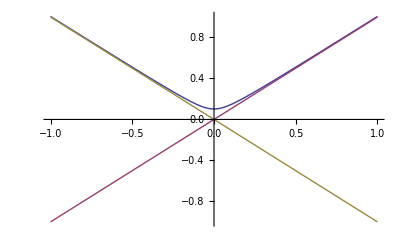

```mathematica
Plot[{w[t]/.{c->1,g->9.8},c*t/.{c->1},-c*t/.{c->1}},{t,-1,1},PlotRange->Full]
```

### Particle Velocity

```mathematica
v[t_]=D[w[t],t]
```

(c^2 t)/(√(c^4/g^2+c^2 t^2))

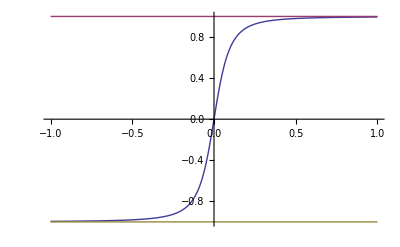

```mathematica
Plot[{v[t]/.{c->1,g->9.8},c/.{c->1},-c/.{c->1}},{t,-1,1}]
```

### Particle Acceleration

```mathematica
a[t_] =D[v[t],t]
```

-(c^4 t^2)/((c^4/g^2+c^2 t^2)^(3/2))+c^2/(√(c^4/g^2+c^2 t^2))

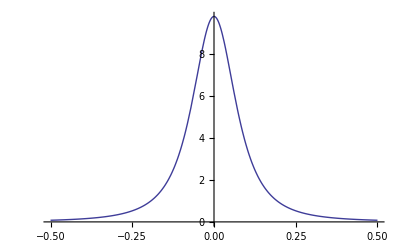

```mathematica
Plot[a[t]/.{c->1,g->9.8},{t,-.5,.5}]
```

```mathematica
Φ[x⃗,t]=[e/((1-β⃗.n̂)*r)]_ret
A⃗[x⃗,t]=[(e*β⃗)/((1-β⃗.n̂)*r)]_ret
r = |x⃗-r⃗(Subscript[τ, 0])|

β⃗ = (v⃗)/c
x⃗ is the field point and r⃗(Subscript[τ, 0]) is the particle position at Subscript[τ, 0]
```

### Scalar Field Φ

```mathematica
e=1
c=1
g=9.8
β[t_]=v[t]/c
Φ[r_,θ_,t_] = e/((1-β[t]*Cos[θ])*r)
```

1

1

9.8

t/(√(0.0104123+t^2))

1/(r (1-(t Cos[θ])/(√(0.0104123+t^2))))

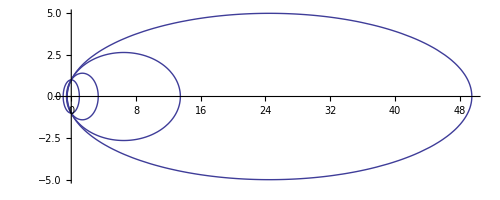

```mathematica
Show[PolarPlot[Φ[r,θ,t]/.{r->1,t->0},{θ,0,2*Pi}],PolarPlot[Φ[r,θ,t]/.{r->1,t->0.1},{θ,0,2*Pi}],PolarPlot[Φ[r,θ,t]/.{r->1,t->0.25},{θ,0,2*Pi}],
PolarPlot[Φ[r,θ,t]/.{r->1,t->0.5},{θ,0,2*Pi}]]
```

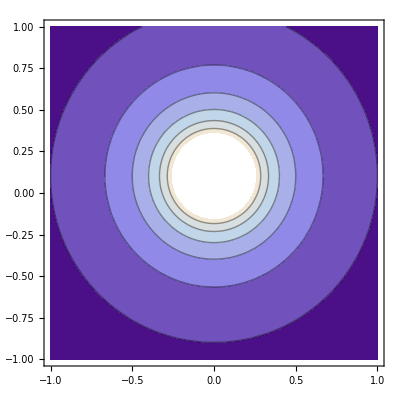

```mathematica
ContourPlot[{e/((1-β[t]*(z-w[t])/(√((z-w[t])^2+x^2)))*√((z-w[t])^2+x^2))}/.{t->0},{x,-1,1},{z,-1,1}]
```

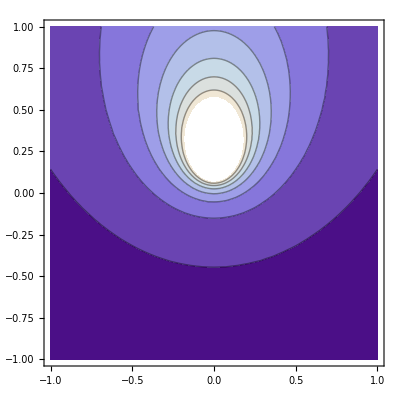

```mathematica
ContourPlot[{e/((1-β[t]*(z-w[t])/(√((z-w[t])^2+x^2)))*√((z-w[t])^2+x^2))}/.{t->0.1},{x,-1,1},{z,-1,1}]
```

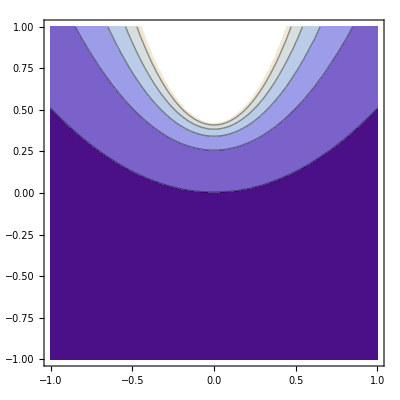

```mathematica
ContourPlot[{e/((1-β[t]*(z-w[t])/(√((z-w[t])^2+x^2)))*√((z-w[t])^2+x^2))}/.{t->0.5},{x,-1,1},{z,-1,1}]
```

### Vector Field A

```mathematica
A[r_,θ_,t_]=(e*β[t])/((1-β[t]*Cos[θ])*r)
```

t/(r √(0.0104123+t^2) (1-(t Cos[θ])/(√(0.0104123+t^2))))

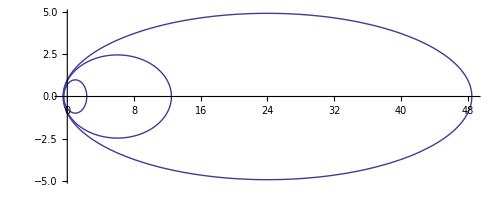

```mathematica
Show[PolarPlot[A[r,θ,t]/.{r->1,t->0},{θ,0,2*Pi}],PolarPlot[A[r,θ,t]/.{r->1,t->0.1},{θ,0,2*Pi}],PolarPlot[A[r,θ,t]/.{r->1,t->0.25},{θ,0,2*Pi}],
PolarPlot[A[r,θ,t]/.{r->1,t->0.5},{θ,0,2*Pi}]]
```

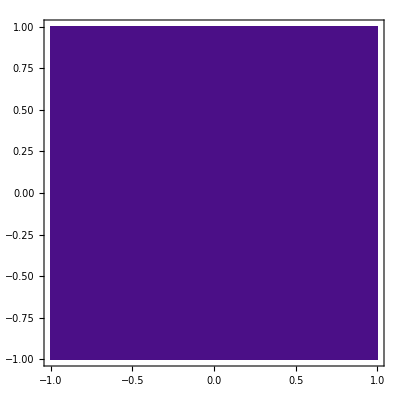

```mathematica
ContourPlot[{(e*β[t])/((1-β[t]*(z-w[t])/(√((z-w[t])^2+x^2)))*√((z-w[t])^2+x^2))}/.{t->0},{x,-1,1},{z,-1,1}]
```

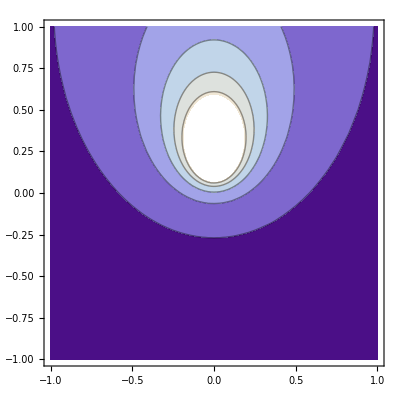

```mathematica
ContourPlot[{(e*β[t])/((1-β[t]*(z-w[t])/(√((z-w[t])^2+x^2)))*√((z-w[t])^2+x^2))}/.{t->0.1},{x,-1,1},{z,-1,1}]
```

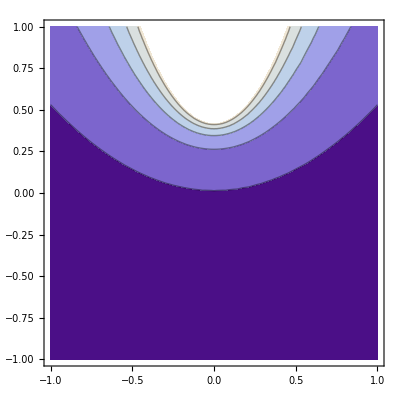

```mathematica
ContourPlot[{(e*β[t])/((1-β[t]*(z-w[t])/(√((z-w[t])^2+x^2)))*√((z-w[t])^2+x^2))}/.{t->0.5},{x,-1,1},{z,-1,1}]
```

```mathematica
E⃗[x⃗,t]=e*[(n̂-β⃗)/(γ^2(1-β⃗.n̂)^3*r^2)]_ret+e/c*[(n̂ x[{n̂-β⃗}*Overscript[β, OverDot[⇀]]])/((1-β⃗.n̂)^3*r)]_ret
B⃗=[n̂ x E⃗]_ret
```

### E Field

```mathematica
Efield[r_,θ_,t_]=e/c*1/((1-β[t]*Cos[θ])^3*r)
```

1/(r (1-(t Cos[θ])/(√(0.0104123+t^2)))^3)

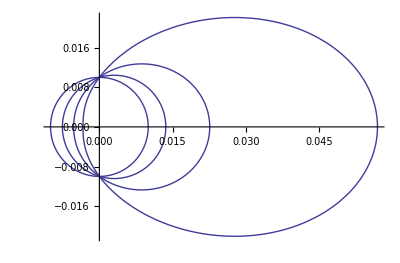

```mathematica
Show[
PolarPlot[Efield[r,θ,t]/.{r->100,t->0},{θ,0,2*Pi}],PolarPlot[Efield[r,θ,t]/.{r->100,t->0.01},{θ,0,2*Pi}],PolarPlot[Efield[r,θ,t]/.{r->100,t->0.025},{θ,0,2*Pi}],PolarPlot[Efield[r,θ,t]/.{r->100,t->0.05},{θ,0,2*Pi}]]
```

```mathematica
in the x-z plane

sinθ= x/(√((z-w[t])^2+x^2))
cosθ=(z-w[t])/(√((z-w[t])^2+x^2))
and r = √((z-w[t])^2+x^2)
where θ is measured with respect to the z-axis
```

```mathematica
ContourPlot[{e/c*1/((1-β[t]*(z-w[t])/(√((z-w[t])^2+x^2)))^3*√((z-w[t])^2+x^2))}/.{t->0},{x,-1,1},{z,-1,1}]
```

-Graphics-

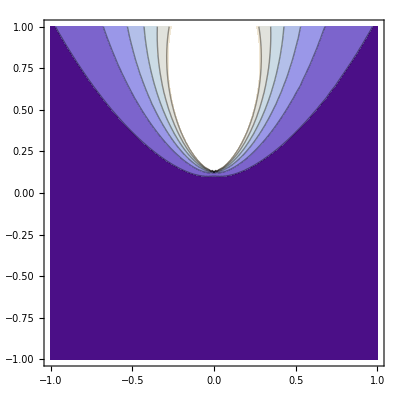

```mathematica
ContourPlot[{e/c*1/((1-β[t]*(z-w[t])/(√((z-w[t])^2+x^2)))^3*√((z-w[t])^2+x^2))}/.{t->0.1},{x,-1,1},{z,-1,1}]
```

### B Field

```mathematica
Bfield[r_,θ_,t_]=e/c*Sin[θ]/((1-β[t]*Cos[θ])^3*r)
```

Sin[θ]/(r (1-(t Cos[θ])/(√(0.0104123+t^2)))^3)

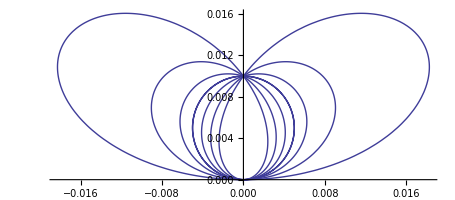

```mathematica
Show[
PolarPlot[Bfield[r,θ,t]/.{r->100,t->0},{θ,0,2*Pi}],PolarPlot[Bfield[r,θ,t]/.{r->100,t->0.01},{θ,0,2*Pi}],PolarPlot[Bfield[r,θ,t]/.{r->100,t->0.025},{θ,0,2*Pi}],PolarPlot[Bfield[r,θ,t]/.{r->100,t->0.05},{θ,0,2*Pi}]]
```

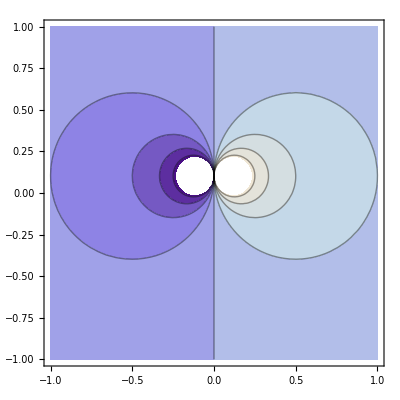

```mathematica
ContourPlot[{e/c*(x/(√((z-w[t])^2+x^2)))/((1-β[t]*(z-w[t])/(√((z-w[t])^2+x^2)))^3*√((z-w[t])^2+x^2))}/.{t->0},{x,-1,1},{z,-1,1}]
```

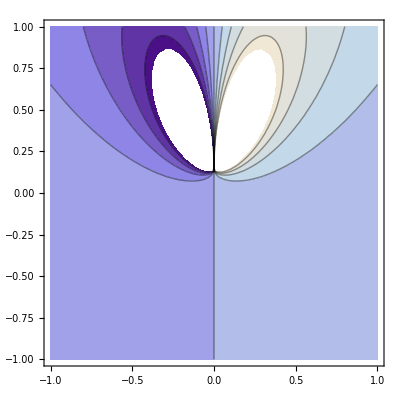

```mathematica
ContourPlot[{e/c*(x/(√((z-w[t])^2+x^2)))/((1-β[t]*(z-w[t])/(√((z-w[t])^2+x^2)))^3*√((z-w[t])^2+x^2))}/.{t->0.1},{x,-1,1},{z,-1,1}]
```

### Poynting Vector

```mathematica
S⃗ =c/(4*Π)*E⃗ x B⃗
```

```mathematica
S[r_,θ_,t_] = c/(4*Pi)*(e/c)^2*(1/((1-β[t]*Cos[θ])^3*r))^2
```

1/(4 π r^2 (1-(t Cos[θ])/(√(0.0104123+t^2)))^6)

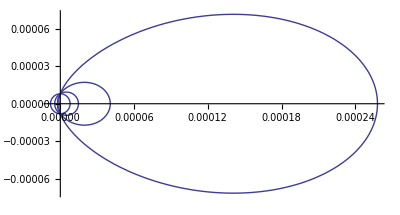

```mathematica
Show[
PolarPlot[S[r,θ,t]/.{r->100,t->0},{θ,0,2*Pi}],PolarPlot[S[r,θ,t]/.{r->100,t->0.01},{θ,0,2*Pi}],PolarPlot[S[r,θ,t]/.{r->100,t->0.025},{θ,0,2*Pi}],PolarPlot[S[r,θ,t]/.{r->100,t->0.05},{θ,0,2*Pi}]]
```